```mathematica
PMatrix = Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/P_Matrix.dat","Table"];
QMatrix = Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/QTil_Matrix.dat","Table"];
energies = Transpose[Import["/Users/niravmehta/Documents/GitHub/AtomIon1D/DiabaticEnergies.dat","Table"]];
RSteps = Dimensions[energies][[2]]
NumStates = Length[PMatrix[[2]]]
```

1000

40

```mathematica
R=energies[[1]];
```

```mathematica
A=1.660539 10^-27;
ma=6.015122 A;
mi=170.936323 A;
ωs=2π 320000;
C4= 1.121 10^-56;
C6=2.804 10^-75;
ℏ=1.054571817 10^-34;
mu2=(ma mi)/(ma+mi)
mu=Sqrt[ma/mi]
thetaC = ArcTan[mu];
aho=Sqrt[ℏ/(ωs mi)]
```

9.64881×10^-27

0.187588

1.35935×10^-8

```mathematica
P = Table[Table[PMatrix[[iR+(iR-1)*NumStates + i]],{i, 1, NumStates}],{iR, 1, RSteps}];
Q = Table[Table[QMatrix[[iR+(iR-1)*NumStates + i]],{i, 1, NumStates}],{iR, 1, RSteps}];
U = Table[energies[[i+1]],{i,1,NumStates}];
```

```mathematica
MatrixList[i_,j_,R_,M_,iRmin_,iRmax_]:=Module[{f},f=Table[{R[[iR]],M[[iR]][[i,j]]},{iR,iRmin,iRmax}]];
UEffList[i_,R_,energies_,Q_,iRmin_,iRmax_] := Module[{f},
f = Table[{R[[iR]],(* U[[i ,iR]] *)-(Q[[iR]][[i,i]])/(2 mu)-(1/4)/(2mu R[[iR]]^2)},{iR,iRmin,iRmax}]]
```

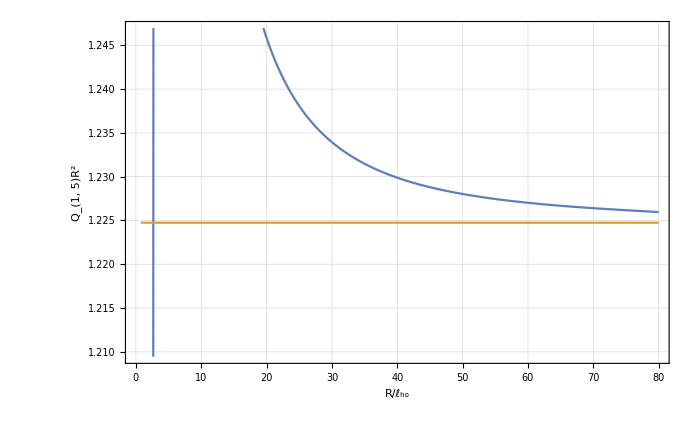

```mathematica
ListPlot[{Table[{R[[iR]],(* U[[i ,iR]] *)Q[[iR]][[1,5]] R[[iR]]^2(*-(1/4)/(2mu R[[iR]]^2)*)},{iR,1,RSteps}],Table[{R[[iR]],√(3/2)},{iR,1,RSteps}]},Frame->True,LabelStyle->Large,GridLines->Automatic,Joined->True,FrameLabel->{"R/ℓ_ho","Q_(1, 5)R^2"}]
```

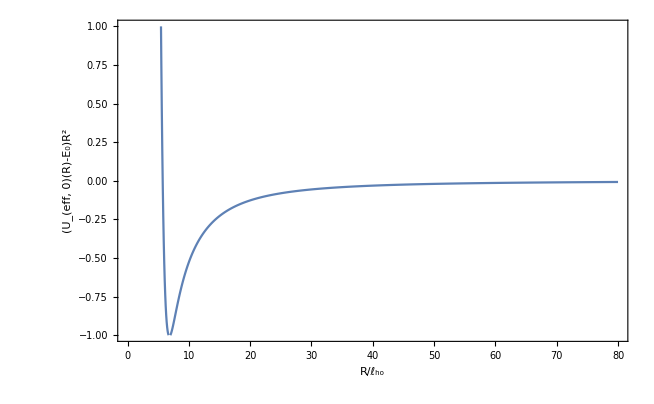

```mathematica
ListPlot[Table[{R[[iR]],( U[[1 ,iR]]-1/2-(Q[[iR]][[1,1]])/(2 mu)-(1/4)/(2mu R[[iR]]^2))R[[iR]]^2 (*-(Q[[iR]][[1,1]])/(2 mu)-(1/4)/(2mu R[[iR]]^2)*)},{iR,1,RSteps}],Joined->True,Frame->True,PlotMarkers->False,PlotRange->{-1,1},LabelStyle->Large,FrameLabel->{"R/ℓ_ho","(U_(eff, 0)(R)-E_0)R^2"}]
```

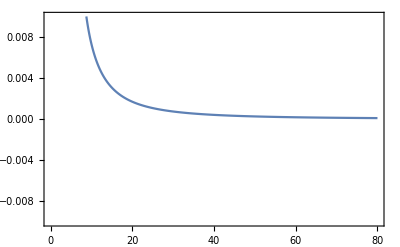

```mathematica
ListPlot[UEffList[1,R,energies,Q,1,RSteps],Joined->True,Frame->True,PlotMarkers->False,PlotRange->{-0.01,0.01}]
```

```mathematica
FindFit[MatrixList[1,1,R,-Q,1,500],a/x^2,a,x]
```

{a→0.50082}

```mathematica
RSteps
```

1000

```mathematica
Dimensions[QMatrix]
```

{41000}

## Older plots for the proposal....

```mathematica
OC=Import["/Users/niravmehta/Library/CloudStorage/GoogleDrive-nmehta@trinity.edu/.shortcut-targets-by-id/1WWtO3hQmjSVv0umtezXAuGjxw_KQ3ycy/Ion-Atom-Trap stuff/Notes/images/Picture1.png"]
```

Import::nffil: File /Users/niravmehta/Library/CloudStorage/GoogleDrive-nmehta@trinity.edu/.shortcut-targets-by-id/1WWtO3hQmjSVv0umtezXAuGjxw_KQ3ycy/Ion-Atom-Trap stuff/Notes/images/Picture1.png not found during Import.

$Failed

```mathematica
TMI=Import["/Users/niravmehta/Library/CloudStorage/GoogleDrive-nmehta@trinity.edu/.shortcut-targets-by-id/1WWtO3hQmjSVv0umtezXAuGjxw_KQ3ycy/Ion-Atom-Trap stuff/Notes/images/Picture2.png"]
```

-Graphics-

```mathematica
AIC=Import["/Users/niravmehta/Library/CloudStorage/GoogleDrive-nmehta@trinity.edu/.shortcut-targets-by-id/1WWtO3hQmjSVv0umtezXAuGjxw_KQ3ycy/Ion-Atom-Trap stuff/Notes/images/Picture3.png"]
```

-Graphics-

```mathematica
PS1=Flatten[{ {{Blue},{Blue},{Blue}},Table[{Black,Thickness[0.002]},{i,4,78}],{{Red},{Red}}},1]
```

{{RGBColor[0, 0, 1]},{RGBColor[0, 0, 1]},{RGBColor[0, 0, 1]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{GrayLevel[0],Thickness[0.002]},{RGBColor[1, 0, 0]},{RGBColor[1, 0, 0]}}

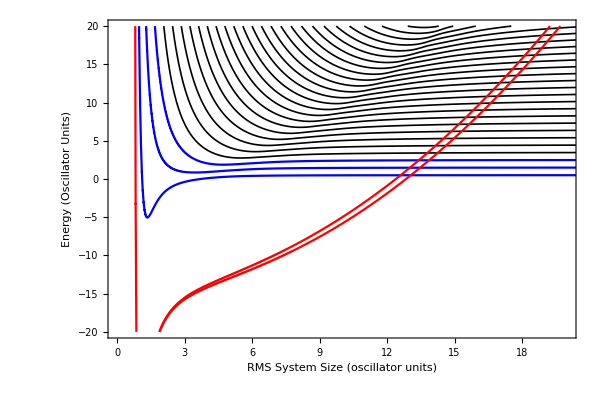

```mathematica
pcurves=ListPlot [Flatten[{UcurvesAll[energies,1,3],UcurvesAll[energies,4,78],UcurvesAll[energies,79,80]},1], PlotStyle->PS1,Joined -> True, Frame -> True, FrameLabel -> {"RMS System Size (oscillator units)","Energy (Oscillator Units)"},ImageSize->{600,400}, LabelStyle-> {Large,Black},PlotRangeClipping->True, PlotRange -> {{0,20},{-20,20}},ImagePadding->{{100,60},{80,10}},AspectRatio->Full]
```

```mathematica
Show[Plot[1/2 x^2,{x,0,20},PlotRange->{{0,20},{-20,20}}],Prolog->{pcurves},Epilog->{Inset[AIC,{3.8,-5}],Inset[TMI,{12,-8.5}],Inset[OC,{20,1}]}]
```

-Graphics-

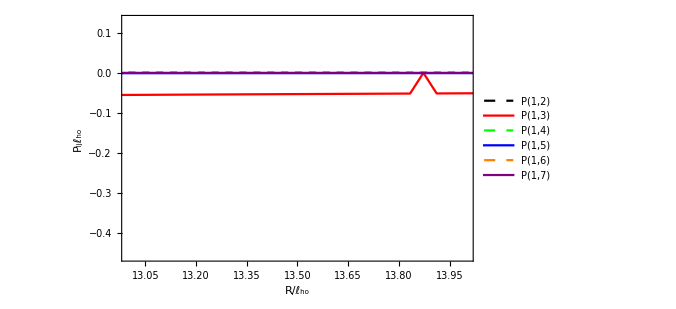

```mathematica
ListPlot[{PlotPog[1,2,R,P],PlotPog[1,3,R,P],PlotPog[1,4,R,P],PlotPog[1,5,R,P],PlotPog[1,6,R,P],PlotPog[1,7,R,P]},  PlotRange->{{13,14},All}, Joined -> True, Frame -> True, FrameLabel -> {"R/ℓ_ho","P_ijℓ_ho"}, PlotLegends->{"P(1,2)","P(1,3)","P(1,4)","P(1,5)","P(1,6)","P(1,7)"}, PlotStyle -> {{Black, Dashed},{Red},{Green,Dashed},{Blue},{Orange,Dashed},{Purple}}, ImageSize -> {500,500},LabelStyle->{Black,Large}]
```

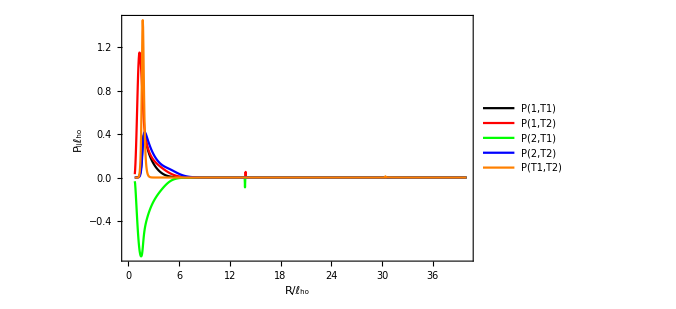

```mathematica
ListPlot[{PlotPog[1,79,R,P],PlotPog[1,80,R,P],PlotPog[2,79,R,P],PlotPog[2,80,R,P],PlotPog[79,80,R,P]},  PlotRange->{{0,40},All}, Joined -> True,PlotMarkers->None, Frame -> True, FrameLabel -> {"R/ℓ_ho","P_ijℓ_ho"}, PlotLegends->{"P(1,T1)","P(1,T2)","P(2,T1)","P(2,T2)","P(T1,T2)","P(1,7)"}, PlotStyle -> {{Black},{Red},{Green},{Blue},{Orange},{Purple}}, ImageSize -> {500,500},LabelStyle->{Black,Large}]
```

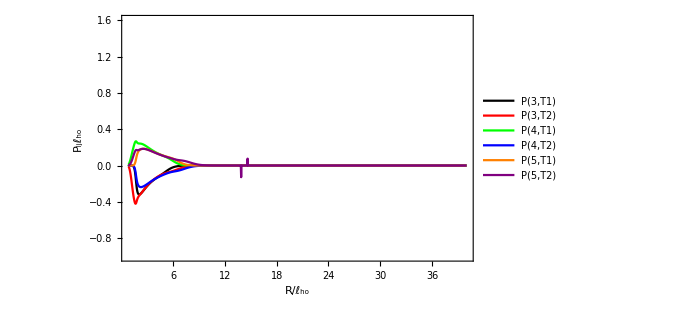

```mathematica
ListPlot[{PlotPog[3,79,R,P],PlotPog[3,80,R,P],PlotPog[4,79,R,P],PlotPog[4,80,R,P],PlotPog[5,79,R,P],PlotPog[5,80,R,P]},  PlotRange->{{0.8,40},{-1,1.6}}, Joined -> True, Frame -> True, FrameLabel -> {"R/ℓ_ho","P_ijℓ_ho"}, PlotLegends->{"P(3,T1)","P(3,T2)","P(4,T1)","P(4,T2)","P(5,T1)","P(5,T2)"}, PlotStyle -> {{Black},{Red},{Green},{Blue},{Orange},{Purple}}, ImageSize -> {500,500},LabelStyle->{Black,Large}]
```

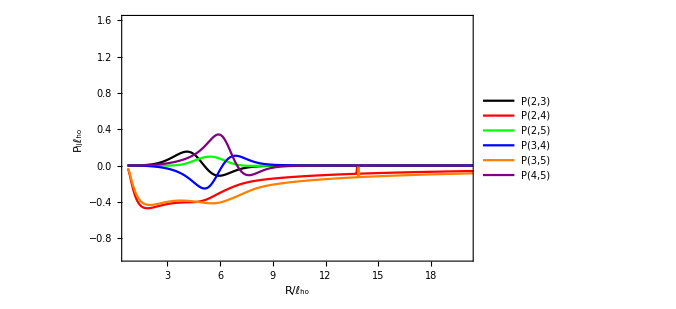

```mathematica
ListPlot[{PlotPog[2,3,R,P],PlotPog[2,4,R,P],PlotPog[2,5,R,P],PlotPog[3,4,R,P],PlotPog[3,5,R,P],PlotPog[4,5,R,P]},  PlotRange->{{0.8,20},{-1,1.6}}, Joined -> True, Frame -> True, FrameLabel -> {"R/ℓ_ho","P_ijℓ_ho"}, PlotLegends->{"P(2,3)","P(2,4)","P(2,5)","P(3,4)","P(3,5)","P(4,5)"}, PlotStyle -> {{Black},{Red},{Green},{Blue},{Orange},{Purple}}, ImageSize -> {500,500},LabelStyle->{Black,Large}]
```